## Panel Plot for sensitivity of trajectories - varying kappa, delta and beta

## Import Data

```mathematica
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
rawKappaLow=Import["export_data/sensi_anal/kappa_low.mat"];
rawKappaHigh=Import["export_data/sensi_anal/kappa_high.mat"];

rawDeltaLow=Import["export_data/sensi_anal/delta_low.mat"];
rawDeltaHigh=Import["export_data/sensi_anal/delta_high.mat"];

rawBetaLow=Import["export_data/sensi_anal/beta_low.mat"];
rawBetaHigh=Import["export_data/sensi_anal/beta_high.mat"];
```

## Function for Grid of Plots

```mathematica
Clear[plotGrid]
plotGrid[l_List,w_,h_,hspace_,vspace_,leftPad_,rightPad_,bottomPad_,topPad_]:=
Module[{nx,ny,
widths,
heights,
dimensions,
positions,
frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},
{ny,nx}=Dimensions[l];
widths=(w-leftPad-rightPad)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+leftPad;
widths[[-1]]=widths[[-1]]+rightPad;
heights=(h-bottomPad-topPad)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+bottomPad;
heights[[-1]]=heights[[-1]]+topPad;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,leftPad+hspace/2,hspace/2],If[i==nx,rightPad+hspace/2,hspace/2]},{If[j==1,bottomPad+vspace/2,vspace/2],If[j==ny,topPad+vspace/2,vspace/2]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Image Options

```mathematica
(* time ticks *)
timeTicks1=Table[{50(i-1),1800+50(i-1)},{i,Range[3,9,2]}]
```

{{100,1900},{200,2000},{300,2100},{400,2200}}

```mathematica
timeTicks=Join[timeTicks1,{{150,""},{250,""},{350,""}}]
```

{{100,1900},{200,2000},{300,2100},{400,2200},{150,},{250,},{350,}}

```mathematica
(* imgs size *)
imgs={200,200};
(* legend position (scaled) *)
legendPos={0.22,0.7};
(* legend marker size *)
lmSize=15;
(* labels (alphabet) *)
labels=Alphabet[];
(* label position (scaled) *)
labelPos={0.05,0.91};
labelSize=10;
(* bold label on off *)
bold=1;
```

```mathematica
{padLeft,padRight,padBottom,padTop}={70,10,30,10};  (* image padding *)
```

```mathematica
(* tick thickness *)
tickThick=0.005;
```

```mathematica
(* time plot range *)
plRange={90,410};
(* social plot range *)
plRangeSoc={-0.02,1.05};
(* emissions plot range *)
plRangeEm={-0.5,18.5};
(* temperature plot range *)
plRangeTemp={-0.1,5.3};
```

```mathematica
(* varying parameter values *)
deltaVals={0,0.5,1,1.5,2,3};
kappaVals={0.01,0.02,0.05,0.1,0.2,100};
```

```mathematica
(* plot line properties *)
line1=Directive[TMBcolours[[1]],Thickness[0.005]];
line2=Directive[TMBcolours[[3]],Thickness[0.005]];

borderLine1=Directive[Opacity[1],Lighter[TMBcolours⟦1⟧,0.8],Thickness[0.005]];
borderLine2=Directive[Opacity[1],Lighter[TMBcolours⟦3⟧,0.8],Thickness[0.005]];
```

```mathematica
(* colour of shading *)
shade1=Directive[Opacity[0.4],Lighter[TMBcolours⟦1⟧,0.8]];
shade2=Directive[Opacity[0.4],Lighter[TMBcolours⟦3⟧,0.8]];
```

```mathematica
(* generic plot options *)
opts={PlotStyle->{borderLine1,borderLine1,line1,borderLine2,borderLine2,line2},
Filling->{1->{{3},shade1},
2->{{3},shade1},
4->{{6},shade2},
5->{{6},shade2}},
ImageSize->imgs,
FrameTicks->{{Automatic,Automatic},{timeTicks,timeTicks}},
FrameTicksStyle->Directive[GrayLevel[0.4],Thickness[tickThick]];
Frame->True,
(*ImagePadding->{{padLeft,padRight},{padBottom,padTop}}*)
LabelStyle->10};
```

## Kappa Plots

### Break up data

```mathematica
(* kappa lower bound *)
tSeries = rawKappaLow[[1,1]];
socSeriesKL = rawKappaLow[[1,2;;]];
emissionSeriesKL=rawKappaLow[[2,2;;]];
tempSeriesKL=rawKappaLow[[3,2;;]];

(* kappa upper bound *)
socSeriesKU = rawKappaHigh[[1,2;;]];
emissionSeriesKU=rawKappaHigh[[2,2;;]];
tempSeriesKU=rawKappaHigh[[3,2;;]];
```

### Make Plots

```mathematica
legendKappa=LineLegend[Table[TMBcolours[[i]],{i,{1,3}}],{"κ=0.02","κ=0.2"},LegendMarkerSize->lmSize]
```

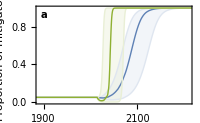

```mathematica
(* proportion of mitigators *)
socPlotKappa=ListLinePlot[{Transpose[{tSeries,socSeriesKL[[1]]}],
Transpose[{tSeries,socSeriesKL[[3]]}],
Transpose[{tSeries,socSeriesKL[[2]]}],
Transpose[{tSeries,socSeriesKU[[1]]}],
Transpose[{tSeries,socSeriesKU[[3]]}],
Transpose[{tSeries,socSeriesKU[[2]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Directive[Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[1]],labelSize,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"Proportion of mitigators",None},{Style["Year",FontOpacity->0],None}},
PlotLegends->Placed[legendKappa,Scaled[legendPos]]]
```

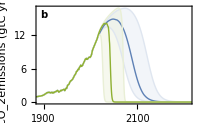

```mathematica
(* emissions *)
emissionPlotKappa=ListLinePlot[{Transpose[{tSeries,emissionSeriesKL[[1]]}],
Transpose[{tSeries,emissionSeriesKL[[3]]}],
Transpose[{tSeries,emissionSeriesKL[[2]]}],
Transpose[{tSeries,emissionSeriesKU[[1]]}],
Transpose[{tSeries,emissionSeriesKU[[3]]}],
Transpose[{tSeries,emissionSeriesKU[[2]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Directive[Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[2]],labelSize,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{Style["Year",FontOpacity->0],None}}]
```

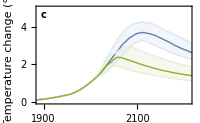

```mathematica
(* temperature plot *)
tempPlotKappa=ListLinePlot[{Transpose[{tSeries,tempSeriesKL[[1]]}],
Transpose[{tSeries,tempSeriesKL[[3]]}],
Transpose[{tSeries,tempSeriesKL[[2]]}],
Transpose[{tSeries,tempSeriesKU[[1]]}],
Transpose[{tSeries,tempSeriesKU[[3]]}],
Transpose[{tSeries,tempSeriesKU[[2]]}]},
PlotRange->{plRange,{0,5}},
opts,
FrameTicksStyle->{{Directive[Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[3]],labelSize,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{Style["Temperature change (°C)",GrayLevel[0.4]],None},{Style["Year",GrayLevel[0.4]],None}}]
```

## Delta Plots

### Break up data

```mathematica
(* kappa lower bound *)
tSeries = rawDeltaLow[[1,1]];
socSeriesDL = rawDeltaLow[[1,2;;]];
emissionSeriesDL=rawDeltaLow[[2,2;;]];
tempSeriesDL=rawDeltaLow[[3,2;;]];

(* kappa upper bound *)
socSeriesDU = rawDeltaHigh[[1,2;;]];
emissionSeriesDU=rawDeltaHigh[[2,2;;]];
tempSeriesDU=rawDeltaHigh[[3,2;;]];
```

### Make Plots

```mathematica
legendDelta=LineLegend[Table[TMBcolours[[i]],{i,{1,3}}],{"δ=0.5","δ=1.5"},LegendMarkerSize->lmSize];
```

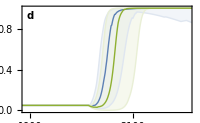

```mathematica
(* proportion of mitigators *)
socPlotDelta=ListLinePlot[{Transpose[{tSeries,socSeriesDL[[1]]}],
Transpose[{tSeries,socSeriesDL[[3]]}],
Transpose[{tSeries,socSeriesDL[[2]]}],
Transpose[{tSeries,socSeriesDU[[1]]}],
Transpose[{tSeries,socSeriesDU[[3]]}],
Transpose[{tSeries,socSeriesDU[[2]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[4]],labelSize,If[bold==1,Bold]],Scaled[labelPos]],
PlotLegends->Placed[legendDelta,Scaled[legendPos]]]
```

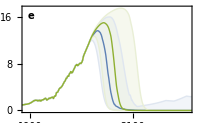

```mathematica
(* emissions *)
emissionPlotDelta=ListLinePlot[{Transpose[{tSeries,emissionSeriesDL[[1]]}],
Transpose[{tSeries,emissionSeriesDL[[3]]}],
Transpose[{tSeries,emissionSeriesDL[[2]]}],
Transpose[{tSeries,emissionSeriesDU[[1]]}],
Transpose[{tSeries,emissionSeriesDU[[3]]}],
Transpose[{tSeries,emissionSeriesDU[[2]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[5]],labelSize,If[bold==1,Bold]],Scaled[labelPos]]]
```

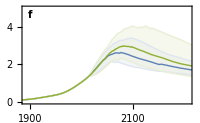

```mathematica
(* temperature plot *)
tempPlotDelta=ListLinePlot[{Transpose[{tSeries,tempSeriesDL[[1]]}],
Transpose[{tSeries,tempSeriesDL[[3]]}],
Transpose[{tSeries,tempSeriesDL[[2]]}],
Transpose[{tSeries,tempSeriesDU[[1]]}],
Transpose[{tSeries,tempSeriesDU[[3]]}],
Transpose[{tSeries,tempSeriesDU[[2]]}]},
PlotRange->{plRange,{0,5}},
opts,
Epilog->Text[Style[labels[[6]],labelSize,If[bold==1,Bold]],Scaled[labelPos]],
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
FrameLabel->{{None,None},{"Year",None}}]
```

## Beta Plots

### Break up data

```mathematica
(* beta lower bound *)
tSeries = rawBetaLow[[1,1]];
socSeriesBL = rawBetaLow[[1,2;;]];
emissionSeriesBL=rawBetaLow[[2,2;;]];
tempSeriesBL=rawBetaLow[[3,2;;]];

(* beta upper bound *)
socSeriesBU = rawBetaHigh[[1,2;;]];
emissionSeriesBU=rawBetaHigh[[2,2;;]];
tempSeriesBU=rawBetaHigh[[3,2;;]];
```

### Make Plots

```mathematica
legendBeta=LineLegend[Table[TMBcolours[[i]],{i,{1,3}}],{"β=0.5","β=1.5"},LegendMarkerSize->lmSize]
```

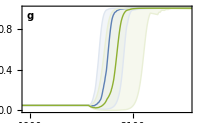

```mathematica
(* proportion of mitigators *)
socPlotBeta=ListLinePlot[{Transpose[{tSeries,socSeriesBL[[1]]}],
Transpose[{tSeries,socSeriesBL[[3]]}],
Transpose[{tSeries,socSeriesBL[[2]]}],
Transpose[{tSeries,socSeriesBU[[1]]}],
Transpose[{tSeries,socSeriesBU[[3]]}],
Transpose[{tSeries,socSeriesBU[[2]]}]},
PlotRange->{plRange,All},
opts,
ImageSize->{ws,hs},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[7]],labelSize,If[bold==1,Bold]],Scaled[labelPos]],
PlotLegends->Placed[legendBeta,Scaled[legendPos]]]
```

```mathematica
(* emissions *)
emissionPlotBeta=ListLinePlot[{Transpose[{tSeries,emissionSeriesBL[[1]]}],
Transpose[{tSeries,emissionSeriesBL[[3]]}],
Transpose[{tSeries,emissionSeriesBL[[2]]}],
Transpose[{tSeries,emissionSeriesBU[[1]]}],
Transpose[{tSeries,emissionSeriesBU[[3]]}],
Transpose[{tSeries,emissionSeriesBU[[2]]}]},
PlotRange->{plRange,All},
opts,
ImageSize->{ws,hs},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0,Black,Thickness[tickThick]],Directive[Black,Thickness[tickThick]]},{Directive[FontOpacity->0,FontSize->0,Black,Thickness[tickThick]],Directive[Black,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[8]],labelSize,If[bold==1,Bold]],Scaled[labelPos]]];
```

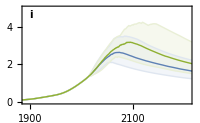

```mathematica
(* temperature plot *)
tempPlotBeta=ListLinePlot[{Transpose[{tSeries,tempSeriesBL[[1]]}],
Transpose[{tSeries,tempSeriesBL[[3]]}],
Transpose[{tSeries,tempSeriesBL[[2]]}],
Transpose[{tSeries,tempSeriesBU[[1]]}],
Transpose[{tSeries,tempSeriesBU[[3]]}],
Transpose[{tSeries,tempSeriesBU[[2]]}]},
PlotRange->{plRange,{0,5}},
opts,
ImageSize->{ws,hb},
FrameLabel->{{None,None},{"Year",None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]],Directive[Thickness[tickThick]]},{Directive[Thickness[tickThick]],Directive[FontOpacity->0,FontSize->0,Thickness[tickThick]]}},
Epilog->Text[Style[labels[[9]],labelSize,If[bold==1,Bold]],Scaled[labelPos]]]
```

```mathematica
Export["figures/tempPlotBeta.tiff",tempPlotBeta,ImageResolution->300,
"ImageEncoding"->"LZW"];
```

## Plot Grid

```mathematica
cm=72/2.54;
```

```mathematica
plotList={{socPlotKappa,socPlotDelta,socPlotBeta},{emissionPlotKappa,emissionPlotDelta,emissionPlotBeta},{tempPlotKappa,tempPlotDelta,tempPlotBeta}};
width=19.05cm;
height=17cm;
vspace=10;
hspace=20;
{{leftPad,rightPad},{bottomPad,topPad}}={{40,10},{40,20}};
```

```mathematica
g1=plotGrid[plotList,width,height,hspace,vspace,leftPad,rightPad,bottomPad,topPad]
```

-Graphics-

```mathematica
Export["figures/figure1.tiff",g1,ImageResolution->600,
"ImageEncoding"->"LZW"];
```